## Lorentz Transformations

Take xa and ta be the distance and time coordinates in the stationary reference frame and xb, tb the distance and time coordinates in the moving in reference frames.

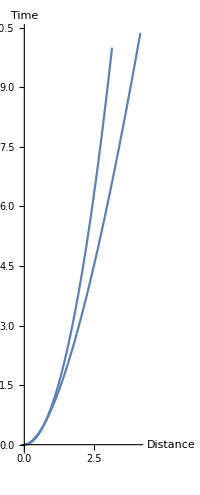

```mathematica
γ = 1/(√(1-v^2));
xb = γ(xa + v ta);
tb = γ (ta + v xa);
xa = √λ;
ta = λ;
ParametricPlot[{{xa,ta},{xb,tb}}/.v->0.1,{λ,0,10}, AxesLabel->{"Distance", "Time"}]
```